# Initialization cells for definitions

```mathematica
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
pblue=RGBColor[1,0,0,0.65];
pyellow=RGBColor[1,1,0,0.65];
pred=RGBColor[173/255,216/255,230/255,0.65];
pgreen=RGBColor[1,0,1,0.65];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Rasterize[Show[g,PlotRangePadding->0,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res]/.Raster[data_,rect_,rest__]:>Raster[data,Transpose@OptionValue[AbsoluteOptions[g,PlotRange],PlotRange],rest],Sequence@@Options[g],Sequence@@Options[g,PlotRange]];
dual[r_]:={r[[2]],-r[[1]]};
CircleArrow[r1_,r2_,ϵ_,off_]:=Arrow[CirclePoints[Mean[{r1,r2}]+ϵ*dual[r2-r1],{Norm[r2-(Mean[{r1,r2}]+ϵ*dual[r2-r1])],ArcTan@@(r2-(Mean[{r1,r2}]+ϵ*dual[r2-r1]))},1000][[1;;Round[1000/(2*Pi)*(ArcTan@@(r1-(Mean[{r1,r2}]+ϵ*dual[r2-r1]))-ArcTan@@(r2-(Mean[{r1,r2}]+ϵ*dual[r2-r1])))]]],off];
graphplot[adj_,dat1_,dat2_,locked1_]:=GraphPlot[adj,DirectedEdges->True,VertexCoordinateRules->Table[k->8*{Cos[2*Pi*k/Length[dat1]],Sin[2*Pi*k/Length[dat1]]},{k,1,M}],EdgeRenderingFunction->({Black,Arrowheads[0.0], CircleArrow[#[[2]],#[[1]],0.1,0.3]} & ),VertexRenderingFunction->({EdgeForm[Black],cf[dat1[[#2]]],If[!MemberQ[locked1,#2],Disk[#,0.3,{-Pi/2,Pi/2}],Rectangle[#-{0.3,0.3},#+{0.0,0.3}]],cf[dat2[[#2]]],If[!MemberQ[locked1,#2],Disk[#,0.3,{Pi/2,3*Pi/2}],Rectangle[#-{0.0,0.3},#+{0.3,0.3}]]}&),ImageSize->300,Epilog->{Inset[ListPlot[{dat1,dat2},PlotRange->All,PlotStyle-> {Directive[PointSize[0.025],Lighter[Red]],Directive[PointSize[0.025],Lighter[Blue]]},Joined->False,Axes->False,Frame->False],{0,0},Scaled[{1/2,1/2}],12]},LabelStyle->Directive[16,Black]];
sci[t_,n_]:=If[t==0,DisplayForm[RowBox[{0}]],DisplayForm[RowBox[{PaddedForm[t/10^Floor[Log[10,t]],{n+1,n}],"e",Floor[Log[10,t]]}]]];
timeplot[phases_]:=rasterizeBackground[MatrixPlot[Transpose[Mod[phases[[All,1;;-1;;Max[1,Round[Length[phases[[1]]]/1000]]]]+Pi,2*Pi]-Pi],ImageSize->{300,300},ImagePadding->{{65,25},{55,15}},DataReversed->{True,False},AspectRatio->1,ColorFunctionScaling->False,ColorFunction->cf,FrameLabel->{DisplayForm[RowBox[{t,"/",t1}]],i},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],DataReversed->{True,False},FrameTicks->{{Table[{i,PaddedForm[(t3+dt*Max[1,Round[Length[phases[[1]]]/1000]]*(i-1))/t1,{2,2}]},{i,1,1001,200}],None},{Table[{i,i/2},{i,0,M,Ceiling[M/5]}],None}},PlotRange->{{1,1001},{1,M+1}}]];
orderplot[orders_]:=ListPlot[orders[[1;;-1;;Max[1,Round[Length[orders]/1000]]]],Joined->True,PlotRange->{0,1},Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{t,"/",t1}]],r},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->{300,300},ImagePadding->{{65,25},{55,15}},AspectRatio->1,FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,1.0,0.2}],None},{Table[{i,PaddedForm[dt*Ceiling[Length[orders]/1000]*(i-1)/t1,{2,1}]},{i,1,1001,200}],None}}]
```

# Plots for single run tests

```mathematica
filebase="data/random/random";
lst=Import[filebase<>"out.dat"];
clusters=Import[filebase<>"clusters.dat"];
{n,t1,t2,t3,dt,avgcount,thrs,β0, β,σ0, σ}=lst[[1,2;;12]];
M=n*2;
ics=lst[[4;;M+3,1]];
times=Table[t,{t,dt,t1,dt}];
Nt=Min[Length/@lst[[4;;M+3]]];
adj=lst[[M+4;;-1]];
orders=lst[[3]];
phases=lst[[4;;M+3]];
dat1=Mod[phases[[1;;-1;;2,1]]+Pi,2*Pi]-Pi;
dat2=Mod[phases[[2;;-1;;2,1]]+Pi,2*Pi]-Pi;
dat3=Mod[phases[[1;;-1;;2,-1]]+Pi,2*Pi]-Pi;
dat4=Mod[phases[[2;;-1;;2,-1]]+Pi,2*Pi]-Pi;
locked1=Flatten[Position[clusters[[1,1;;M;;2]],0.]];
locked2=Flatten[Position[clusters[[-1,1;;M;;2]],0.]];
p1=orderplot[orders];
p2=timeplot[phases];
p3=Show[graphplot[adj,dat1,dat2,locked1],Prolog->Inset[Style[DisplayForm[RowBox[{"t=",t3}]],16],{0,5}]];
p4=Show[graphplot[adj,dat3,dat4,locked2],Prolog->Inset[Style[DisplayForm[RowBox[{"t=",t1}]],16],{0,5}]];
Legended[Grid[{{p1,p2},{p3,p4}}],Placed[MatrixPlot[Table[cf[-Pi+2*Pi*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,-Pi},{25,DisplayForm[RowBox[{-Pi,"/",2}]]},{50,0},{75,DisplayForm[RowBox[{"π","/",2}]]},{100,Pi}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/20,ImageSize->250,PlotLabel->θ,PlotRange->{{1,10},{1,100}}],Below]]
```

-Graphics-

# Plots for adiabatic branch sweeps

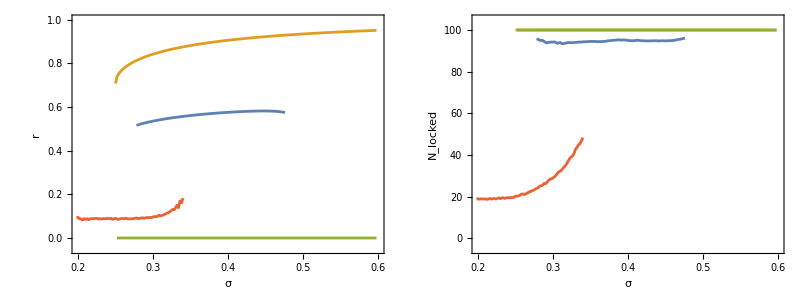

```mathematica
filebases={"data/branches/chimera","data/branches/sync","data/branches/twisted","data/branches/async"};
orders=Join[If[FileExistsQ[#<>"currentorder.dat"],Import[#<>"currentorder.dat"],{}],If[FileExistsQ[#<>"sweep.dat"],Import[#<>"sweep.dat"],{}]]&/@filebases;
Grid[{{ListPlot[SortBy[#,First]&/@orders[[All,All,{1,3}]],PlotRange->{{0.2,0.6},{-0.05,1}},ImageSize->400,Axes->False,Frame->True,FrameLabel->{"σ",r},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],Joined->True,PlotStyle->Directive[AbsoluteThickness[2.0]]],ListPlot[SortBy[#,First]&/@orders[[All,All,{1,4}]],PlotRange->{{0.2,0.6},{-5,105}},ImageSize->400,Axes->False,Frame->True,FrameLabel->{"σ",Subscript["N","locked"]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],Joined->True,PlotStyle->Directive[AbsoluteThickness[2.0]]]}}]
```